Sensitivity Analysis - Tornado Plots

## Setup

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Baseline Parameter Values along with lower and upper bounds

### Parameter Labels

```mathematica
(* parameter labels *)
parLabels={"f_0","χ","ζ","x_0","κ","δ","β","f_max","ω","T_c","t_f","C_at0","C_oc0","C_ve0","C_so0","k_p","k_r","k_t","k_sr","k_c","k_M","E_a","k_MM","k_A","k_B","S","A","τ(CH_4)","P_0","c","s"};
numParams=Length[parLabels];
```

```mathematica
parDefs={"Ocean flux rate constant","Characteristic CO_2 solubility","Evasion factor","Initial proportion of mitigators","Social learning rate","Strength of social norms","Cost of mitigation","Maximum of warming cost function","Nonlinearity of warming cost function","Critical temperature of warming cost function","Time horizon of temperature projection","Pre-industrial CO_2 in atmosphere","Pre-industrial CO_2 in ocean","Pre-industrial CO_2 in vegetation","Pre-industrial CO_2 in soil","Photosynthesis rate constant","Plant respiration constant","Turnover rate constant","Soil respiration rate constant","Photosynthesis compensation point","Half-saturation point for photosynthesis","Plant respiration activation energy","Photosynthesis normalising constant","Plant respiration normalising constant","Soil respiration normalising constant","Solar flux","Surface albedo","Methane opacity","Water vapour saturation constant","Specific heat capacity of Earth's surface","Half-saturation time for ϵ(t)"};
```

```mathematica
{parLabels,parDefs}//Transpose//TableForm
```

f_0 | Ocean flux rate constant
χ | Characteristic CO_2 solubility
ζ | Evasion factor
x_0 | Initial proportion of mitigators
κ | Social learning rate
δ | Strength of social norms
β | Cost of mitigation
f_max | Maximum of warming cost function
ω | Nonlinearity of warming cost function
T_c | Critical temperature of warming cost function
t_f | Time horizon of temperature projection
C_at0 | Pre-industrial CO_2 in atmosphere
C_oc0 | Pre-industrial CO_2 in ocean
C_ve0 | Pre-industrial CO_2 in vegetation
C_so0 | Pre-industrial CO_2 in soil
k_p | Photosynthesis rate constant
k_r | Plant respiration constant
k_t | Turnover rate constant
k_sr | Soil respiration rate constant
k_c | Photosynthesis compensation point
k_M | Half-saturation point for photosynthesis
E_a | Plant respiration activation energy
k_MM | Photosynthesis normalising constant
k_A | Plant respiration normalising constant
k_B | Soil respiration normalising constant
S | Solar flux
A | Surface albedo
τ(CH_4) | Methane opacity
P_0 | Water vapour saturation constant
c | Specific heat capacity of Earth's surface
s | Half-saturation time for ϵ(t)

### Muryshev parameters

```mathematica
f0B=2.5*^-2; (* ocean flux constant (2.5-4.5 *10^-2) *)
{f0L,f0U}={0.9f0B,1.1f0B};
chiB=0.3; (* characterisitc co2 solubility in seawater (lower->higher temp anomaly) *)
{chiL,chiU}={0.2,0.4};
zetaB=50; (* buffer factor (higher-> reduces total carbon storage of ocean - long term temp higher *)
{zetaL,zetaU}={40,60};
```

### Social parameters

```mathematica
x0B=0.05; (* proportion of mitigators in 2010 *)
{x0L,x0U}={0.5x0B,1.5x0B};
κB=0.05; (* social learning rate *)
{κL,κU} = {0.02,0.1};
δB=1; (* strength of social norms *)
{δL,δU}={0.5,1.5};
βB=1; (* cost of adopting mitigatve strategies *)
{βL,βU}={0.5,1.5};
(* response function to temp *)
omegaB=3;
{omegaL,omegaU}={1,5};
tempThreshB=2.5;
{tempThreshL,tempThreshU}={2.4,2.6};
fmaxB=5;
{fmaxL,fmaxU}={4,6};
resType=1; (* 1 sigmoidal, 2 linear *)

(* temp prediction (linear extrapolation from previous temperatures) *) 
tempProjOnOff=1; (* on 1, off 0 *)
deltatPastB=10; (* based on previous number of years *)
deltatFutB=25; (* years looking ahead *)
{deltatFutL,deltatFutU}={10,40};
```

### Conversion factors

```mathematica
ka=1.773*^20; (* moles in atmosphere *)
gtcToMol=8.3259*^13;(* factor from gtC to moles *)
gtcToPpm=gtcToMol*10^6/ka; (* factor from gtc to ppmv *)
gtcTogtco2=3.664; (* factor from gtC from gtCO2 *)
secondstoyrs=60*60*24*365; (* factor from seconds to years *)
```

### Initial conditions (pre-industrial)

```mathematica
cat0B=596; (* initial carbon in the atmostphere *)
{cat0L,cat0U}={cat0B-6,cat0B+6};
coc0B=1.5*^5; (* initial carbon in the ocean *)
{coc0L,coc0U}={1.4*^5,1.6*^5};
cve0B=550; (* initial carbon in veg *)
{cve0L,cve0U}={cve0B-10,cve0B+10};
cso0B=1500; (*initical carbon in soil *)
{cso0L,cso0U}={cso0B-20,cso0B+20};
temp0B=288.15; (* inital temp *)
```

### Lenton parameters

```mathematica
kpB=0.184; (* photosyn rate *)
{kpL,kpU}={0.95*kpB,1.05*kpB};
krB=0.092; (*plant respiration rate *)
{krL,krU}={0.9*krB,1.1*krB};
ktB=0.092; (* turnover rate *)
{ktL,ktU}={0.9*ktB,1.1*ktB};
ksrB=0.0337; (* soil respiration rate *)
{ksrL,ksrU}={0.9*ksrB,1.1*ksrB};
kcB=29*^-6; (* compensation point *)
{kcL,kcU}={0.9*kcB,1.1*kcB};
kMB=120*^-6; (* half-saturation point - set to 145 for ocean warming *)
{kML,kMU}={0.9*kMB,1.1*kMB};
```

```mathematica
eaB=54830; (* plant respiration activation energy *)
{eaL,eaU}={54630,54830};
kMMB=1.478; (* photosyn normalising constnat - set to 1.578 for ocean warming *)
{kMML,kMMU}={0.9*kMMB,1.1*kMMB};
kAB=8.7039*^9; (* plant respiration normalising constant &*)
{kAL,kAU}={0.9*kAB,1.1*kAB};
kBB=157.072; (* soil respiration normalising constant*)
{kBL,kBU}={0.9*kBB,1.1*kBB};
solarB=1368; (* solar flux *)
{solarL,solarU}={0.9*solarB,1.1*solarB};
albedoB=0.225; (* surface albedo *)
{albedoL,albedoU}={0.9*albedoB,1.1*albedoB};
tauch4B=0.0231; (* methane opacity *)
{tauch4L,tauch4U}={0.9*tauch4B,1.1*tauch4B};
p0B=1.4*^11; (* water vapour saturation constant *)
{p0L,p0U}={0.9*p0B,1.1*p0B};
(* humidity parameter is fit to give pre-industrial steady state temperature of T=288.15K as in Lenton00 *)
capB=4.69*^23; (* specific heat capacity *)
{capL,capU}={0.9*capB,1.1*capB};
```

### Universal parameters

```mathematica
rgas=8.314; (* universal gas constant *)
lheat=43655; (* latent heat per mole of water *)
σ=5.67*^-8; (* Stefan-Boltzman constant*)
aE=5.101*^14; (* earth SA *)
```

### Emission parameter

```mathematica
sB=50; (* half saturation time of global energy demands *)
{sL,sU}={30,70};
```

## Parameter Configurations

```mathematica
(* Muryshev params *)
f0Vals={f0L,f0B,f0U};
chiVals={chiL,chiB,chiU};
zetaVals={zetaL,zetaB,zetaU};
(* Social params *)
x0Vals={x0L,x0B,x0U};
κVals={κL,κB,κU};
δVals={δL,δB,δU};
βVals={βL,βB,βU};
fmaxVals={fmaxL,fmaxB,fmaxU};
omegaVals={omegaL,omegaB,omegaU};
tempThreshVals={tempThreshL,tempThreshB,tempThreshU};
deltatFutVals={deltatFutL,deltatFutB,deltatFutU};
(* initial sinks *)
cat0Vals={cat0L,cat0B,cat0U};
coc0Vals={coc0L,coc0B,coc0U};
cve0Vals={cve0L,cve0B,cve0U};
cso0Vals={cso0L,cso0B,cso0U};
(* lenton parameters *)
kpVals={kpL,kpB,kpU};
krVals={krL,krB,krU};
ktVals={ktL,ktB,ktU};
ksrVals={ksrL,ksrB,ksrU};
kcVals={kcL,kcB,kcU};
kMVals={kML,kMB,kMU};
eaVals={eaL,eaB,eaU};
kMMVals={kMML,kMMB,kMMU};
kAVals={kAL,kAB,kAU};
kBVals={kBL,kBB,kBU};
solarVals={solarL,solarB,solarU};
albedoVals={albedoL,albedoB,albedoU};
tauch4Vals={tauch4L,tauch4B,tauch4U};
p0Vals={p0L,p0B,p0U};
capVals={capL,capB,capU};
(* global energy demand parameter *)
sVals={sL,sB,sU};
```

```mathematica
(* set up configurations *)
Clear[fun]
fun[i_,j_]:=ReplacePart[Table[2,{q,1,numParams}],i->j]
```

```mathematica
config=Table[fun[i,j],{i,1,numParams},{j,1,3}];
```

```mathematica
(* array of parameter bounds *)
parBounds={f0Vals,chiVals,zetaVals,x0Vals,κVals,δVals,βVals,fmaxVals,omegaVals,tempThreshVals,deltatFutVals,cat0Vals,coc0Vals,cve0Vals,cso0Vals,kpVals,krVals,ktVals,ksrVals,kcVals,kMVals,eaVals,kMMVals,kAVals,kBVals,solarVals,albedoVals,tauch4Vals,p0Vals,capVals,sVals};
```

## Run system up to year 2014 with baseline param values

### Assign baseline values

```mathematica
(* ocean *)
f0=f0B;
chi=chiB;
zeta=zetaB;

(* social *)
x0=x0B;
κ=κB;
δ=δB;
β=βB;
fmax=fmaxB;
omega=omegaB;
tempThresh=tempThreshB;

deltatPast=deltatPastB; (* based on previous number of years *)
deltatFut=deltatFutB; (* years looking ahead *)

(* initial carbon values *)
cat0=cat0B;
coc0=coc0B;
cve0=cve0B;
cso0=cso0B;
temp0=temp0B;

(* Lenton parameters *)
kp=kpB;
kr=krB;
kt=ktB;
ksr=ksrB;
kc=kcB;
kM=kMB;
ea=eaB;
kMM=kMMB;
kA=kAB;
kB=kBB;
solar=solarB;
albedo=albedoB;
tauch4=tauch4B;
p0=p0B;
cap=capB;

(* emission parameter *)
s=sB;
```

### Functional Forms

```mathematica
(* OCEAN DYNAMICS *)

(* carbon flux to ocean from atmosphere *)
Clear[foc];
foc[temp_,cat_,coc_]:=f0*chi*(cat-zeta*cat0*coc/coc0);

(* LAND DYNAMICS *)

(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a];
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka;
(* photosynthesis - from Lenton *)
Clear[photo]
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
(* respiration of plants *)
Clear[respp];
respp[temp_,cve_]:=kr*(cve+cve0)*kA*Exp[-(ea/(rgas*(temp+temp0)))];
(* turnover of plants *)
Clear[turnover];
turnover[cve_]:=kt*(cve+cve0);
(* respiration of soil *)
Clear[resps];
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))];
(* carbon flux to land from atmosphere *)
Clear[fla];
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];

(* ATMOSPHERE DYANMICS *)

(* opacity of co2 *)
Clear[tauco2];
tauco2[ca_]:=1.73*pco2a[ca]^0.263;
(* opacity of h20 *)
Clear[hum];
Clear[tauh2o];
tauh2o[temp_,hum_]:=0.0126*(hum*p0*Exp[-lheat/(rgas*(temp+temp0))])^0.503;
(* total opacity *)
Clear[tau];
tau[ca_,temp_,hum_]:=tauco2[ca]+tauh2o[temp,hum]+tauch4;
(* downward flux of radiation *)
Clear[fd];
fd[ca_,temp_,hum_]:=((1-albedo)*solar/4)*(1+3tau[ca,temp,hum]/4);
(* Calibrate hum so that equilibirum temperature of 288.15K in 1800 *)
hum=humidity/.Quiet[Solve[fd[0,0,humidity]-σ temp0^4==0,humidity]][[1]];

(* EMISSION DATA *)
(* historical emissions from Lenton *)
emissionData={{0,0.35},{50,0.4},{147,2},{180,6.7},{190,7.4},{200,8.5},{210,10.0}};
futureEmissionData={{215,10.6},{220,11.4},{225,12.2},{250,14.5},{275,16.3},{300,20.3},{400,0},{1200,0}};

(* make future emisssion function that continues from data, and saturates *)
linIncr=(10.6-8.5)/15; (* obtained from previous emission data *)
emax=s*linIncr;

Clear[futureEmissionFun3];
futureEmissionFun3[t_]:=((t-215) emax)/(t-215+s)+10.6;
emissions=Interpolation[Union[emissionData,futureEmissionData],InterpolationOrder->1];
Clear[emissions3];
emissions3[t_]:=Which[t≤215,emissions[t],t>215,futureEmissionFun3[t]];


(* SOCIAL DYNAMICS *)
(* social response to temperature function *)
Clear[resSig,resLin]
resSig[temp_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
resLin[temp_]:=fmax/5*temp;
(* assign response function *)
Clear[res]
Which[resType==1,res[temp_]:=resSig[temp],
resType==2,res[temp_]:=resLin[temp]];
```

### Run Dynamics

```mathematica
(* Clear variable names *)
Clear[cat,coc,cve,cso,temp,soc,t];

(* Run from t=0 to tcurrnet *)
tStep=0.1;
tcurrent=214; (* year 2020 *)
tmax=tcurrent;

(* Run evolution equations with baseline parameter values up to 2020 *)
sim1=NDSolve[{cat'[t]==emissions3[t](1-soc[t])/(1-x0)-foc[temp[t],cat[t],coc[t]]-fla[cat[t],cve[t],cso[t],temp[t]],
coc'[t]==foc[temp[t],cat[t],coc[t]],
cve'[t]==photo[cat[t],temp[t]]-respp[temp[t],cve[t]]-turnover[cve[t]],
cso'[t]==turnover[cve[t]]-resps[temp[t],cso[t]],
temp'[t]==secondstoyrs*(aE/cap)*(fd[cat[t],temp[t],hum]-σ (temp[t]+temp0)^4),
soc'[t]==Which[0≤t≤tcurrent,0,
t>tcurrent && tempProjOnOff==1,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]+(deltatFut/deltatPast)*(temp[t]-temp[t-deltatPast])]+(δ*(2soc[t]-1))),
t>tcurrent && tempProjOnOff==0,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]]+(δ*(2soc[t]-1)))],
cat[t/;t≤0]==0,
coc[t/;t≤0]==0,
cve[t/;t≤0]==0,
cso[t/;t≤0]==0,
temp[t/;t≤0]==0,
soc[t/;t≤0]==x0},
{cat,coc,cve,cso,temp,soc},
{t,0,tmax}];

(* obtain series functions *)
Clear[catSeriesPre,cocSeriesPre,cveSeriesPre,csoSeriesPre,tempSeriesPre,socSeriesPre,emissionsSeriesPre];
catSeriesPre[t_]:=cat[t]/.sim1[[1]];
cocSeriesPre[t_]:=coc[t]/.sim1[[1]];
cveSeriesPre[t_]:=cve[t]/.sim1[[1]];
csoSeriesPre[t_]:=cso[t]/.sim1[[1]];
tempSeriesPre[t_]:=temp[t]/.sim1[[1]];
socSeriesPre[t_]:=soc[t]/.sim1[[1]];
emissionsSeriesPre[t_]:=emissions3[t]*(1-socSeriesPre[t]);


(* Put into data form *)
catPreData=Table[catSeriesPre[t],{t,0,tmax,tStep}];
cocPreData=Table[cocSeriesPre[t],{t,0,tmax,tStep}];
cvePreData=Table[cveSeriesPre[t],{t,0,tmax,tStep}];
csoPreData=Table[csoSeriesPre[t],{t,0,tmax,tStep}];
tempPreData=Table[tempSeriesPre[t],{t,0,tmax,tStep}];
socPreData=Table[socSeriesPre[t],{t,0,tmax,tStep}];
emissionsPreData=Table[emissionsSeriesPre[t],{t,0,tmax,tStep}];
```

## For Loop Over Parameter configurations for Tornado Plot

```mathematica
(* Clear functions *)
Clear[tempAnomaly]; (* function to capture temperature anomolies : has form (parameter varied, parameter value (lower, base, upper)) *)
```

### For Loop

```mathematica
Clear[i,j]
```

```mathematica
parLabels
```

{f_0,χ,ζ,x_0,κ,δ,β,f_max,ω,T_c,t_f,C_at0,C_oc0,C_ve0,C_so0,k_p,k_r,k_t,k_sr,k_c,k_M,E_a,k_MM,k_A,k_B,S,A,τ(CH_4),P_0,c,s}

```mathematica
(* function to find index of parameter *)
Clear[indexPar]
indexPar[param_]:=Position[parLabels,param][[1,1]];
```

```mathematica
For[i=1,i≤Dimensions[config][[1]],i++, (* loop over different parameter values being varied *)
For[j=1,j≤Dimensions[config][[2]],j++, (* loop over lower, base, upper values of parameter *)

(* ASSIGN PARAMETER VALUES CONFIGURATIONS *)

(* Muryshev params *)
f0=f0Vals[[config[[i,j,indexPar["f_0"]]]]];
chi=chiVals[[config[[i,j,indexPar["χ"]]]]];
zeta=zetaVals[[config[[i,j,indexPar["ζ"]]]]];
(* Social params *)
x0=x0Vals[[config[[i,j,indexPar["x_0"]]]]];
κ=κVals[[config[[i,j,indexPar["κ"]]]]];
δ=δVals[[config[[i,j,indexPar["δ"]]]]];
β=βVals[[config[[i,j,indexPar["β"]]]]];
fmax=fmaxVals[[config[[i,j,indexPar["f_max"]]]]];
omega=omegaVals[[config[[i,j,indexPar["ω"]]]]];
tempThresh=tempThreshVals[[config[[i,j,indexPar["T_c"]]]]];
deltatFut=deltatFutVals[[config[[i,j,indexPar["t_f"]]]]];
(* initial sink values *)
cat0=cat0Vals[[config[[i,j,indexPar["C_at0"]]]]];
coc0=coc0Vals[[config[[i,j,indexPar["C_oc0"]]]]];
cve0=cve0Vals[[config[[i,j,indexPar["C_ve0"]]]]];
cso0=cso0Vals[[config[[i,j,indexPar["C_so0"]]]]];
(* lenton parameters *)
kp=kpVals[[config[[i,j,indexPar["k_p"]]]]];
kr=krVals[[config[[i,j,indexPar["k_r"]]]]];
kt=ktVals[[config[[i,j,indexPar["k_t"]]]]];
ksr=ksrVals[[config[[i,j,indexPar["k_sr"]]]]];
kc=kcVals[[config[[i,j,indexPar["k_c"]]]]];
kM=kMVals[[config[[i,j,indexPar["k_M"]]]]];
ea=eaVals[[config[[i,j,indexPar["E_a"]]]]];
kMM=kMMVals[[config[[i,j,indexPar["k_MM"]]]]];
kA=kAVals[[config[[i,j,indexPar["k_A"]]]]];
kB=kBVals[[config[[i,j,indexPar["k_B"]]]]];
solar=solarVals[[config[[i,j,indexPar["S"]]]]];
albedo=albedoVals[[config[[i,j,indexPar["A"]]]]];
tauch4=tauch4Vals[[config[[i,j,indexPar["τ(CH_4)"]]]]];
p0=p0Vals[[config[[i,j,indexPar["P_0"]]]]];
cap=capVals[[config[[i,j,indexPar["c"]]]]];
(* global energy demand parameter *)
s=sVals[[config[[i,j,indexPar["s"]]]]];



(* OCEAN DYNAMICS *)

(* carbon flux to ocean from atmosphere *)
Clear[foc];
foc[temp_,cat_,coc_]:=f0*chi*(cat-zeta*cat0*coc/coc0);

(* LAND DYNAMICS *)

(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a];
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka;
(* photosynthesis - from Lenton *)
Clear[photo];
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
(* respiration of plants *)
Clear[respp];
respp[temp_,cve_]:=kr*(cve+cve0)*kA*Exp[-(ea/(rgas*(temp+temp0)))];
(* turnover of plants *)
Clear[turnover];
turnover[cve_]:=kt*(cve+cve0);
(* respiration of soil *)
Clear[resps];
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))];
(* carbon flux to land from atmosphere *)
Clear[fla];
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];

(* ATMOSPHERE DYANMICS *)

(* opacity of co2 *)
Clear[tauco2];
tauco2[ca_]:=1.73*pco2a[ca]^0.263;
(* opacity of h20 *)
Clear[hum];
Clear[tauh2o];
tauh2o[temp_,hum_]:=0.0126*(hum*p0*Exp[-lheat/(rgas*(temp+temp0))])^0.503;
(* total opacity *)
Clear[tau];
tau[ca_,temp_,hum_]:=tauco2[ca]+tauh2o[temp,hum]+tauch4;
(* downward flux of radiation *)
Clear[fd];
fd[ca_,temp_,hum_]:=((1-albedo)*solar/4)*(1+3tau[ca,temp,hum]/4);
(* Calibrate hum so that equilibirum temperature of 288.15K in 1800 *)
hum=humidity/.Quiet[Solve[fd[0,0,humidity]-σ temp0^4==0,humidity]][[1]];

(* EMISSION DATA *)
(* historical emissions from Lenton *)
emissionData={{0,0.35},{50,0.4},{147,2},{180,6.7},{190,7.4},{200,8.5},{210,10.0}};
futureEmissionData={{215,10.6},{220,11.4},{225,12.2},{250,14.5},{275,16.3},{300,20.3},{400,0},{1200,0}};

(* make future emisssion function that continues from data, and saturates *)
linIncr=(10.6-8.5)/15; (* obtained from previous emission data *)
emax=s*linIncr;

Clear[futureEmissionFun3];
futureEmissionFun3[t_]:=((t-215) emax)/(t-215+s)+10.6;
emissions=Interpolation[Union[emissionData,futureEmissionData],InterpolationOrder->1];
Clear[emissions3];
emissions3[t_]:=Which[t≤215,emissions[t],t>215,futureEmissionFun3[t]];


(* SOCIAL DYNAMICS *)

(* social response to temperature function *)
Clear[resSig,resLin];
resSig[temp_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
resLin[temp_]:=fmax/5*temp;
(* assign response function *)
Clear[res];
Which[resType==1,res[temp_]:=resSig[temp],
resType==2,res[temp_]:=resLin[temp]];


(* RUN DYNAMICS *)

(* Clear variable names *)
Clear[cat,coc,cve,cso,temp,soc];

(* Max time *)
tmax=600;

(* Run evolution equations from t=tcurrent (=220) to t=tmax  *)
sim2=NDSolve[{cat'[t]==emissions3[t](1-soc[t])/(1-x0)-foc[temp[t],cat[t],coc[t]]-fla[cat[t],cve[t],cso[t],temp[t]],
coc'[t]==foc[temp[t],cat[t],coc[t]],
cve'[t]==photo[cat[t],temp[t]]-respp[temp[t],cve[t]]-turnover[cve[t]],
cso'[t]==turnover[cve[t]]-resps[temp[t],cso[t]],
temp'[t]==secondstoyrs*(aE/cap)*(fd[cat[t],temp[t],hum]-σ (temp[t]+temp0)^4),
soc'[t]==Which[0≤t≤tcurrent,0,
t>tcurrent && tempProjOnOff==1,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]+(deltatFut/deltatPast)*(temp[t]-temp[t-deltatPast])]+(δ*(2soc[t]-1))),
t>tcurrent && tempProjOnOff==0,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]]+(δ*(2soc[t]-1)))],
cat[t/;t≤tcurrent]==catSeriesPre[t],
coc[t/;t≤tcurrent]==cocSeriesPre[t],
cve[t/;t≤tcurrent]==cveSeriesPre[t],
cso[t/;t≤tcurrent]==csoSeriesPre[t],
temp[t/;t≤tcurrent]==tempSeriesPre[t],
soc[t/;t≤tcurrent]==socSeriesPre[t]},
{cat,coc,cve,cso,temp,soc},
{t,tcurrent,tmax}];


(* obtain series functions *)
Clear[catSeries,cocSeries,cveSeries,csoSeries,tempSeries,socSeries,emissionSeries];
catSeries[t_]:=cat[t]/.sim2[[1]];
cocSeries[t_]:=coc[t]/.sim2[[1]];
cveSeries[t_]:=cve[t]/.sim2[[1]];
csoSeries[t_]:=cso[t]/.sim2[[1]];
tempSeries[t_]:=temp[t]/.sim2[[1]];
socSeries[t_]:=soc[t]/.sim2[[1]];
emissionSeries[t_]:=emissions3[t]*(1-socSeries[t]);

(* assign maximum temperature to function tempMax *)
tempAnomaly[i,j]=NMaximize[{tempSeries[t],tcurrent≤t≤tmax},t,Method->"SimulatedAnnealing"][[1]];
]
]
```

## Create Tornado Plot

### Choose from list of parameters which to vary for tornado plot

```mathematica
(* display parameters and corresponding numbers and values *)
{Range[1,numParams],parLabels,parDefs,parBounds}//Transpose//MatrixForm
```

(1 | f_0 | Ocean flux rate constant | {0.0225,0.025,0.0275}
2 | χ | Characteristic CO_2 solubility | {0.2,0.3,0.4}
3 | ζ | Evasion factor | {40,50,60}
4 | x_0 | Initial proportion of mitigators | {0.025,0.05,0.075}
5 | κ | Social learning rate | {0.02,0.05,0.1}
6 | δ | Strength of social norms | {0.5,1,1.5}
7 | β | Cost of mitigation | {0.5,1,1.5}
8 | f_max | Maximum of warming cost function | {4,5,6}
9 | ω | Nonlinearity of warming cost function | {1,3,5}
10 | T_c | Critical temperature of warming cost function | {2.4,2.5,2.6}
11 | t_f | Time horizon of temperature projection | {10,25,40}
12 | C_at0 | Pre-industrial CO_2 in atmosphere | {590,596,602}
13 | C_oc0 | Pre-industrial CO_2 in ocean | {140000.,150000.,160000.}
14 | C_ve0 | Pre-industrial CO_2 in vegetation | {540,550,560}
15 | C_so0 | Pre-industrial CO_2 in soil | {1480,1500,1520}
16 | k_p | Photosynthesis rate constant | {0.1748,0.184,0.1932}
17 | k_r | Plant respiration constant | {0.0828,0.092,0.1012}
18 | k_t | Turnover rate constant | {0.0828,0.092,0.1012}
19 | k_sr | Soil respiration rate constant | {0.03033,0.0337,0.03707}
20 | k_c | Photosynthesis compensation point | {0.0000261,29/1000000,0.0000319}
21 | k_M | Half-saturation point for photosynthesis | {0.000108,3/25000,0.000132}
22 | E_a | Plant respiration activation energy | {54630,54830,54830}
23 | k_MM | Photosynthesis normalising constant | {1.3302,1.478,1.6258}
24 | k_A | Plant respiration normalising constant | {7.83351×10^9,8.7039×10^9,9.57429×10^9}
25 | k_B | Soil respiration normalising constant | {141.365,157.072,172.779}
26 | S | Solar flux | {1231.2,1368,1504.8}
27 | A | Surface albedo | {0.2025,0.225,0.2475}
28 | τ(CH_4) | Methane opacity | {0.02079,0.0231,0.02541}
29 | P_0 | Water vapour saturation constant | {1.26×10^11,1.4×10^11,1.54×10^11}
30 | c | Specific heat capacity of Earth's surface | {4.221×10^23,4.69×10^23,5.159×10^23}
31 | s | Half-saturation time for ϵ(t) | {30,50,70})

```mathematica
parList=Delete[Range[1,31],{{23},{24},{25}}];
```

```mathematica
(*parList={5,6,7,8,9};*)
```

```mathematica
(* baseline temp value *)
baseTempAnomaly=tempAnomaly[1,2];
```

```mathematica
(* data for tornado plot *)
tempAnomalyData=Table[Join[Table[tempAnomaly[i,j],{j,1,3}],{parLabels[[i]],parDefs[[i]]}],{i,parList}];
```

```mathematica
(* Sort parameters by how sensitive temp anomaly is to thems *)
```

```mathematica
tempAnomalyDataSort=SortBy[tempAnomalyData,Max[Abs[#-baseTempAnomaly]]&];
```

```mathematica
(* parameter deviations *)
lowerParDevs=Table[tempAnomalyDataSort[[i,1]],{i,1,Length[tempAnomalyDataSort]}]-baseTempAnomaly;
upperParDevs=Table[tempAnomalyDataSort[[i,3]],{i,1,Length[tempAnomalyDataSort]}]-baseTempAnomaly;
```

```mathematica
(* maximum deviation *)
maxDev=Max[Flatten[Join[lowerParDevs,upperParDevs]]]
```

0.648941

```mathematica
(* ticks to shift deviation scale to actual temperatur scale *)
tornadoTicks=Table[{i-baseTempAnomaly,i},{i,0,7,0.5}];

(* vis options for plot *)
opts={BarOrigin->Left,
PlotRange->{{-maxDev-0.1,maxDev+0.1},All},
FrameTicks->{{Range[1,numParams],Range[1,numParams]},{tornadoTicks,None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
FrameLabel->{{"",""},{"Peak Temperature Anomaly (°C)",""}},
LabelStyle->14,
ImagePadding->{{50,250},{50,10}},
ImageSize->650,
AspectRatio->1.8};
```

```mathematica
plot1=BarChart[lowerParDevs,
opts,
Frame->{{True,True},{True,False}},
PlotRangeClipping->False,
ChartStyle->TMBcolours[[1]],
Epilog->{Table[Text[Style[tempAnomalyDataSort[[i,4]],12],Scaled[{-0.025,0.054+0.948/Length[parList](i-1)}],{1,0}],{i,1,Length[parList]}],
Table[Text[Style[tempAnomalyDataSort[[i,5]],12],Scaled[{1.025,0.054+0.948/Length[parList](i-1)}],{-1,0}],{i,1,Length[parList]}]},
GridLines->{None,Range[1,numParams]}];
```

```mathematica
plot2=BarChart[upperParDevs,
Axes->False,
ChartStyle->TMBcolours[[4]],
opts];
```

```mathematica
tornadoPlot=Show[{plot1,plot2}];
```

## Output

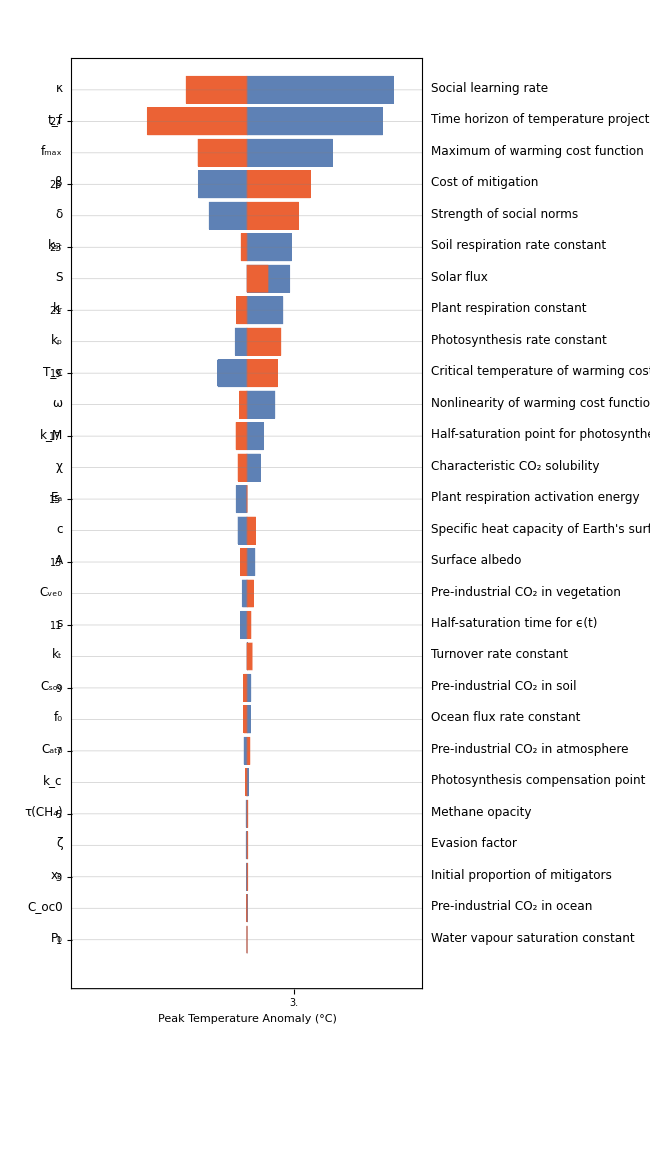

```mathematica
tornadoPlot
```

```mathematica
(*Export["figures/fig_tornado.png",tornadoPlot,ImageResolution->200];*)
```